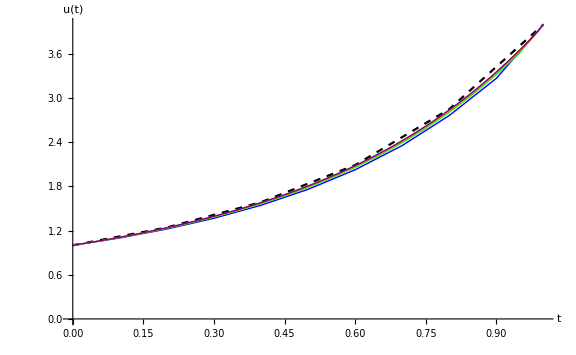

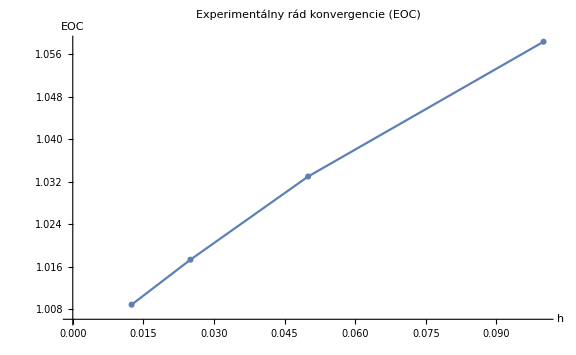

```mathematica
exactSolution=DSolve[{u''[t]==12 t^2+2,u'[0]==1,u[1]==4},u,t];
exactFunc[t_]=u[t]/. First[exactSolution];

data5=Import["C:\\Users\\Asus ROG Strix G15\\STUBA\\Rocnik_2\\Letny_semester\\NRODR\\Cvicenie_11\\solution_h_5.csv","Data","HeaderLines"->1];
data10=Import["C:\\Users\\Asus ROG Strix G15\\STUBA\\Rocnik_2\\Letny_semester\\NRODR\\Cvicenie_11\\solution_h_10.csv","Data","HeaderLines"->1];
data20=Import["C:\\Users\\Asus ROG Strix G15\\STUBA\\Rocnik_2\\Letny_semester\\NRODR\\Cvicenie_11\\solution_h_20.csv","Data","HeaderLines"->1];
data40=Import["C:\\Users\\Asus ROG Strix G15\\STUBA\\Rocnik_2\\Letny_semester\\NRODR\\Cvicenie_11\\solution_h_40.csv","Data","HeaderLines"->1];
data80=Import["C:\\Users\\Asus ROG Strix G15\\STUBA\\Rocnik_2\\Letny_semester\\NRODR\\Cvicenie_11\\solution_h_80.csv","Data","HeaderLines"->1];

plots=ListLinePlot[{{#[[1]],exactFunc[#[[1]]]}&/@data5,{#[[1]],#[[2]]}&/@data5},PlotLegends->{"Presné riešenie","Numerické h=1/5"},PlotStyle->{Red,Blue},PlotLabel->"Porovnanie presného a numerických riešení",AxesLabel->{"t","u(t)"},ImageSize->Large];

combinedPlot=Show[ListLinePlot[{#[[1]],exactFunc[#[[1]]]}&/@data5,PlotStyle->{Dashed,Black}],ListLinePlot[{#[[1]],#[[2]]}&/@data10,PlotStyle->{Thick,Blue}],ListLinePlot[{#[[1]],#[[2]]}&/@data20,PlotStyle->{Thick,Green}],ListLinePlot[{#[[1]],#[[2]]}&/@data40,PlotStyle->{Thick,Orange}],ListLinePlot[{#[[1]],#[[2]]}&/@data80,PlotStyle->{Thick,Purple}],PlotLegends->{"Exact","h=1/5","h=1/10","h=1/20","h=1/40","h=1/80"},AxesLabel->{"t","u(t)"},ImageSize->Large];

GraphicsGrid[{{plots,combinedPlot}},ImageSize->Full]

eocData=Import["C:\\Users\\Asus ROG Strix G15\\STUBA\\Rocnik_2\\Letny_semester\\NRODR\\Cvicenie_11\\eoc_results.csv","Data","HeaderLines"->1];
eocPlot=ListLinePlot[eocData,PlotMarkers->Automatic,PlotLabel->"Experimentálny rád konvergencie (EOC)",AxesLabel->{"h","EOC"},Joined->True,ImageSize->Large];

eocPlot
```